## Task 2 List Generation

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task2_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

```mathematica
dataList=Table[StringTake[data[[i]],6],{i,1,Length[data]}];
```

{{110100,2877},{010101,2845},{011100,2808},{011101,276},{001100,79},{100100,69},{000101,86},{110001,7},{011000,73},{010100,60},{110101,297},{111100,283},{010001,87},{110000,86},{100110,1},{001010,10},{111000,8},{101100,6},{001101,3},{011001,6},{100101,7},{000100,2},{000011,10},{100010,6},{000111,1},{010000,1},{101010,1},{001011,2},{000001,1},{001000,1},{100000,1}}

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
000001 | 1
000111 | 1
001000 | 1
010000 | 1
100000 | 1
100110 | 1
101010 | 1
000100 | 2
001011 | 2
001101 | 3
011001 | 6
100010 | 6
101100 | 6
100101 | 7
110001 | 7
111000 | 8
000011 | 10
001010 | 10
010100 | 60
100100 | 69
011000 | 73
001100 | 79
000101 | 86
110000 | 86
010001 | 87
011101 | 276
111100 | 283
110101 | 297
011100 | 2808
010101 | 2845
110100 | 2877

## Task1-2 (The bit-string order is Reversed!)

```mathematica
graph={{0.3461717838632017,1.4984640297338632},{0.6316400411846113,2.5754677320579895},{1.3906262250927481,2.164978861396621},{0.66436005100802,0.6717919819739032},{0.8663329771713457,3.3876341010035995},{1.1643107343501296,1.0823066243402013}}
```

{{0.346172,1.49846},{0.63164,2.57547},{1.39063,2.16498},{0.66436,0.671792},{0.866333,3.38763},{1.16431,1.08231}}

```mathematica
labels={"1","2","3","4","5","6"};
```

```mathematica
solutions={{1,3,5},{3,4,5},{3,5,6}};
solLabels={"101010","001110","001011"};
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=1;
color1=Lighter[Gray];
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1]};bList={#}&/@graph;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph[[#]],T]}&/@Table[i,{i,1,6}];
dots={Black,Disk[graph[[#]],0.05]}&/@Table[i,{i,1,6}];
Graphics[Flatten[{circles,dots},1],Frame->True,FrameTicks->None,PlotLabel->Style[ToString[solLabels[[i1]]],Bold,25,Black]]]
```

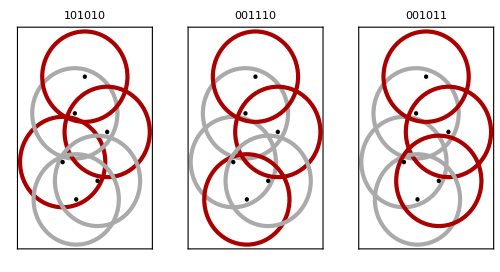

```mathematica
GraphicsRow[{plot[1],plot[2],plot[3]},ImageSize->500]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
Export["101010c.jpg",plot[1]]
Export["001110c.jpg",plot[2]]
Export["001011c.jpg",plot[3]]
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

101010c.jpg

001110c.jpg

001011c.jpg

## Task 3 List Generation

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task3_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

```mathematica
dataList=Table[StringTake[data[[i]],12],{i,1,Length[data]}];
```

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
000000011011 | 1
000001000011 | 1
000001000110 | 1
000001011011 | 1
000010010001 | 1
000010011011 | 1
000011000011 | 1
000011000100 | 1
000100010001 | 1
000100011000 | 1
000101011001 | 1
000111000110 | 1
001000011011 | 1
001001010011 | 1
001100011001 | 1
010000011000 | 1
010000101011 | 1
010000110011 | 1
010000111001 | 1
010001000100 | 1
010001011011 | 1
010010011001 | 1
010100011001 | 1
010101010001 | 1
011000000001 | 1
011000001011 | 1
011000001100 | 1
011000010001 | 1
011000100011 | 1
011000100110 | 1
011001000011 | 1
011001000110 | 1
011100011001 | 1
100000010001 | 1
100000100001 | 1
100000100010 | 1
100000101011 | 1
100001000010 | 1
100001000100 | 1
100001000111 | 1
100001011001 | 1
100011000011 | 1
100011000110 | 1
100011011001 | 1
100100010011 | 1
100100011001 | 1
100101000110 | 1
101000010000 | 1
101000011010 | 1
101001000110 | 1
101010010011 | 1
110000011001 | 1
110001000110 | 1
110001010000 | 1
110001010001 | 1
110001010010 | 1
111000000001 | 1
111000000010 | 1
111000010000 | 1
111000010001 | 1
111000010010 | 1
111000011000 | 1
000010010011 | 2
000100011011 | 2
000101000011 | 2
010000001001 | 2
010000011011 | 2
011000000010 | 2
011000010000 | 2
100000011011 | 2
100000111001 | 2
100001100110 | 2
111000001001 | 2
000000011001 | 3
000011010001 | 3
000100010011 | 3
000110011001 | 3
100010011001 | 3
111000000110 | 3
111000011011 | 3
010000100110 | 4
010101000110 | 4
100000010011 | 4
111001010011 | 4
000101010001 | 5
010001011001 | 5
101000000011 | 5
010000010011 | 6
100001010010 | 6
010001010001 | 7
101000011000 | 7
010000100011 | 8
100000100110 | 8
101000001001 | 8
010001010010 | 9
011000000011 | 9
100001010001 | 9
101000010001 | 10
011000011000 | 11
100000011001 | 14
100000100011 | 14
100001000011 | 17
101000000110 | 17
001000011001 | 19
010001000011 | 19
010001000110 | 19
011000000110 | 19
011000001001 | 20
010000011001 | 23
100001000110 | 23
010000101001 | 25
111000011001 | 25
010011010011 | 26
100000101001 | 26
000101000110 | 27
011000010010 | 27
100101010011 | 28
101000010010 | 30
000011000110 | 32
100011010011 | 33
000010011001 | 35
000111010011 | 36
001000010011 | 37
010101010011 | 38
101000011011 | 45
111000010011 | 49
000100011001 | 51
011000011011 | 53
110001010011 | 56
101001010011 | 90
011001010011 | 99
000001010011 | 125
011000011001 | 283
101000011001 | 292
000101010011 | 964
000011010011 | 974
011000010011 | 1255
101000010011 | 1276
100001010011 | 1753
010001010011 | 1772

## Task 2 Visualization (The bit-string order is Reversed!)

```mathematica
graph1={{1.19,4.25},{2.71,3.48},{1.19,3.51},{2,3.38},{1.12,2.86},{1.70,2.42},{2.36,2.54},{1.52,1.48},{2.15,1.54},{2.14,1.87},{1.72,0.86},{2.29,0.87}};
solLabels={"011000010011","101000010011","100001010011","010001010011"};
Do[f[j]={},{j,1,4}];
Do[If[StringPart[solLabels[[j]], i]=="1",f[j]=Append[f[j],13-i]],{i,1,12},{j,1,4}]
solutions=Table[f[j],{j,1,4}]
```

{{11,10,5,2,1},{12,10,5,2,1},{12,7,5,2,1},{11,7,5,2,1}}

```mathematica
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=0.72;
color1=Lighter[Gray];
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1]};bList={#}&/@graph;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,12}];
dots={Black,Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,12}];
Graphics[Flatten[{circles,dots},1],Frame->True,FrameTicks->None,PlotLabel->Style[ToString[solLabels[[i1]]],Bold,25,Black]]]
```

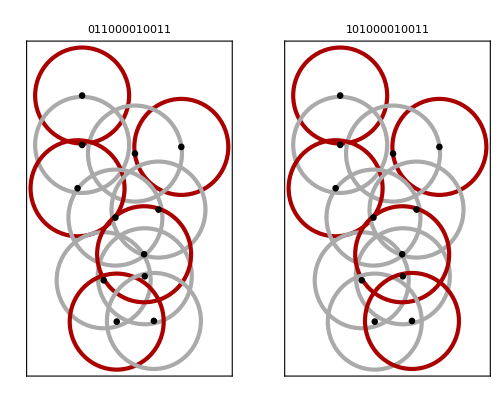

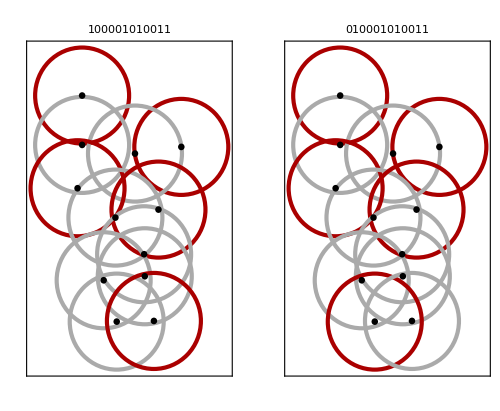

```mathematica
GraphicsRow[{plot[1],plot[2]},ImageSize->500]
GraphicsRow[{plot[3],plot[4]},ImageSize->500]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
Export["011000010011c.jpg",plot[1]]
Export["101000010011c.jpg",plot[2]]
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

011000010011c.jpg

101000010011c.jpg